```mathematica
Incoherent Charge Transport under strong matter-light coupling in organic microcavities
```

-coupling in light microcavities organic+Charge Incoherent matter strong Transport under

```mathematica
c[n_,m_]:=Binomial[n,m];
comb[N_,k_]:=Subsets[Table[i,{i,1,N}],{k}];
Num[x_]:=N[x];
(*Dropp[Ds_,elem_]:=Drop[Ds,{Position[Ds,elem][[1,1]]}];*)
Dropp[Ds_,elem_]:=Complement[Ds,{elem}];(*compared to old above def, complement also removes repetition, but that is not present in our case unless something is wrong! *)

HgMap[N_,k_]:=Module[{tab,ind1,listi,tabx,sites,flipsites,set1,flip,listf,xb,xa},
tab={};tabx={};
listi=comb[N,k];
sites=Table[i,{i,1,N}];
Do[
set1=listi[[i]];
flipsites=Complement[sites,set1];
Do[
flip=flipsites[[j]];
listf=Sort[Join[set1,{flip}]];
xa=c[N,k+1]-Sum[c[N-listf[[p+1]],k+1-p],{p,0,k}];
AppendTo[tabx,xa];
,{j,1,Length[flipsites]}];
AppendTo[tab,tabx];tabx={};
,{i,1,Length[listi]}];
tab] 

makeHg[N_,m_,gg_]:=Module[
{pntr,ind1,ind2,coora,ntot,Hg,ind2sub,m1},

(* seperate case with saturated polarisation *)
m1=Min[m,N];(*If[m≤ N,m1=m,m1=N];*)
(* pointers for start index *)
pntr=Insert[Table[Sum[c[N,j],{j,0,i}],{i,0,m1}],0,1];
ntot=pntr[[-1]];
Hg=SparseArray[{},{ntot,ntot}];
Do[
ind1=pntr[[k+1]]+Table[i,{i,1,c[N,k]}];
ind2=pntr[[k+2]]+HgMap[N,k];
(*Print[HgMap[N,k]];*)
coora={};
Do[ind2sub=ind2[[j]];
Do[AppendTo[coora, {ind1[[j]],ind2sub[[j2]]}];
,{j2,1,Length[ind2sub]}];
,{j,1,Length[ind1]}];
(* caution: Sqrt[m-k]*gg contains m, not m1 *)
Hg+=SparseArray[coora-> Sqrt[m-k]*gg,{ntot,ntot}];
,{k,0,m1-1}];
Hg//Num
];

DiagH[N_,m_,gg_]:=Module[{Hg,eval,U,Uct},
If[m>0,
Hg=makeHg[N,m,gg];Hg+=Transpose[Hg];
(* Sort, ascending order:
ref: https://stackoverflow.com/questions/6589005/sort-eigenvalue-matrix-with-eigenvector-matrix *)
{eval,U}=Transpose@SortBy[Transpose[Eigensystem[Hg]],First];
,
(* make E&U by hand *)
eval={0.0};U={{1.0}};
];
{eval,U}
];
```

```mathematica
(* (D,Phi) + A -> A' *)

(* (D,Phi)+A[m,N] -> A[m+1,N+2] *)
(* map of indices of states when a D,Phi pair combines to make two singly occupied sites *)

(* N=0 case *)
makeHtDPhiAN0[m_,thh_,tll_]:=Module[
{ntot1,Htsp,ntot2},
(* init basis states = 1 *)
ntot1=1;
(* Final basis states:|00,m+1>,|10,m>,|01,m>,|11,m-1>; last only if m>0 *)
ntot2=If[m==0,3,4];
(*Only middle two states couple to the init state of D,Phi *)
Htsp=SparseArray[{{1,2}-> thh,{1,3}-> tll},{ntot1,ntot2}];
Htsp
];

(* D&Phi sites turning to active go to the end of active list.*)
mapDPhiA[N_,k_]:=Module[{x,ind1,ind2,listi,tab1,tab2,set1,listf},
tab1={};tab2={};
listi=comb[N,k];
Do[
set1=listi[[i]];
listf=Sort[Join[set1,{N+1}]];(* Lexicographical ordering! *)
x=c[N+2,k+1]-Sum[c[N+2-listf[[p+1]],k+1-p],{p,0,k}];
(* only when (D,Phi) -> (up,down); when they go to (down,up), add 1 in the indices, this is done when this map is used *)
AppendTo[tab1,x];(*AppendTo[tab2,x+1];*)
,{i,1,Length[listi]}];
tab1];

(* only a sub-block (ntot1 x ntot2) of full Ht (ntot x ntot) *)
makeHtDPhiA[N_,m_,thh_,tll_]:=Module[
{pntr1,pntr2,Hta,Htb,ind1,ind2,ind2a,ind2b,coora,coorb,ntot1,Htsp,ntot2,Hg,ind2sub,ind1reptd,m1,m2},

If[N==0,Htsp=makeHtDPhiAN0[m,thh,tll],
(* pointers for start index *)
m1=Min[m,N];m2=Min[m+1,N+2];
pntr1=Insert[Table[Sum[c[N,j],{j,0,i}],{i,0,m1}],0,1];
ntot1=pntr1[[-1]];
pntr2=Insert[Table[Sum[c[N+2,j],{j,0,i}],{i,0,m2}],0,1];
ntot2=pntr2[[-1]];
(* maps all sectors (up spins); Ht *)
Hta={};Htb={};
Do[
ind1={pntr1[[k+1]]+Table[i,{i,1,c[N,k]}]}//Transpose;
ind2=pntr2[[k+2]]+mapDPhiA[N,k]; (* shift k by 1 *)
ind2a={ind2}//Transpose; (* th: (D,Phi) -> (up,down) *)
ind2b={ind2 +1}//Transpose; (* tl: (D,Phi) -> (down,up) *)
If[Length[ind1]>0,
coora=Join[ind1,ind2a,2];AppendTo[Hta,coora ];
coorb=Join[ind1,ind2b,2];AppendTo[Htb,coorb ];
];
,{k,0,m1}];
Htsp=SparseArray[Flatten[Hta,1]-> thh,{ntot1,ntot2}]+SparseArray[Flatten[Htb,1]-> tll,{ntot1,ntot2}];
];
Htsp
];


(* mapHtApairs: for Apairs that can make D & Phi: start with final basis combination and add two sites at appropriate positions in the list of active sites with one being up and other down, and calc index for initial state *)

mapHtApairs[N_,k_,sapos_]:=Module[
{n1,n2,x1,x2,listi1,listi2,tab1,tab2,set1,set2,listf1,listf2,set11,set12}
,
{n1,n2}=sapos;
tab1={};tab2={};
(* (N-2,k-1), add desired up/dn or dn/up to make (N,k) *)
(* exclude k=0 case *)
If[k>0,
listi1=comb[N-2,k-1]; 
Do[
set1=listi1[[i]];
(* add an up site at n1 position
and a down at n2 position; shift n1+ and n2+ labels by 1 or 2 as they should be *)
(* shift by +1 twice for second case means +2 total as desired *)
set11=set1/.{q_Integer/;q≥ n1->q+1};
set12=set11/.{q_Integer/;q≥ n2->q+1};
(* Adding up/down  at n1/n2*)
listf1=Sort[Join[set11,{n1}]];
(* Adding down/up  at n1/n2*)
listf2=Sort[Join[set11,{n2}]];
(* indices for (N,k) case *)
x1=c[N,k]-Sum[c[N-listf1[[p+1]],k-p],{p,0,k-1}];
x2=c[N,k]-Sum[c[N-listf2[[p+1]],k-p],{p,0,k-1}];
AppendTo[tab1,x1];
AppendTo[tab2,x2];
,{i,1,Length[listi1]}];
];
{tab1,tab2}
];

makeHtApairs[N_,m_,sapos_,th_,tl_,f_]:=Module[
{pntr0,pntr1,ntot0,Hta,Htb,coora,coorb,ntot1,tab1,tab2,ind1,ind01,ind02,t1,t2,Htsp,m1,m2,m3},
(* v v importnat: in  sapos, n2>n1 *)
(* pointers for start index *)
m1=Min[m,N];m2=Min[m-1,N-2];m3=Min[m,N-1];
pntr0=Insert[Table[Sum[c[N,j],{j,0,i}],{i,0,m1}],0,1];
pntr1=Insert[Table[Sum[c[N-2,j],{j,0,i}],{i,0,m2}],0,1];
ntot0=pntr0[[-1]];
ntot1=pntr1[[-1]];
Hta={};Htb={};
(* k loop up to m3=Min[m,N-1] so that 
there is always a down spin available for non-empty map;
starts from 1, so for an up spin available *)
Do[
(* indices list of initial states *)
{tab1,tab2}=mapHtApairs[N,k,sapos];
ind01={pntr0[[k+1]]+tab1}//Transpose;
ind02={pntr0[[k+1]]+tab2}//Transpose;
ind1={pntr1[[k]]+Table[i,{i,1,c[N-2,k-1]}]}//Transpose;
If[Length[tab1]>0,coora=Join[ind01,ind1,2];AppendTo[Hta,coora ];];
If[Length[tab2]>0,coorb=Join[ind02,ind1,2];AppendTo[Htb,coorb ];];
,{k,1,m3}];
(*Htsph=SparseArray[Flatten[Hta,1]-> 1,{ntot0,ntot1}]; (* tl + f*th ; f = e^(-βE.r) panelty for hopping to left against the applied bias; E elec field, r intersite distance *)
Htspl=SparseArray[Flatten[Htb,1]-> 1,{ntot0,ntot1}]; (* f*tl + th  *)
*)
t1=tl + f*th;
t2=f*tl + th;
Htsp=SparseArray[Flatten[Hta,1]-> t1,{ntot0,ntot1}]+
SparseArray[Flatten[Htb,1]-> t2,{ntot0,ntot1}];
Htsp
];
```

```mathematica
(* D|Phi + A -> D'|Phi' +A' *)
(* active site number n interacting with D/Phi *)

DiagHt4DA[N_,k_,n_,th_,tl_]:=Module[{tab,listi},
listi=comb[N,k];
tab={};
(*Print[" DiagHt4DA --------------"];*)
If[k>0,
Do[
(*Print[" DiagHt4DA,i=",i];*)
If[MemberQ[listi[[i]],n],AppendTo[tab,th],AppendTo[tab,tl]];
,{i,1,Length[listi]}];
,
AppendTo[tab,tl];
];
tab];

mkHtDA[N_,m_,n_,th_,tl_]:=Module[{HtdiagDA},
(* make Ht diagonal array for all up spin sectors *)
HtdiagDA={};
(*Print[" mkHtDA --------------"];*)
Do[
AppendTo[HtdiagDA,DiagHt4DA[N,k,n,th,tl]];
,{k,0,Min[m,N]}];
HtdiagDA=Flatten[HtdiagDA];
DiagonalMatrix[HtdiagDA]
];
mkHtPhiA[N_,m_,n_,th_,tl_]:=Module[{HtdiagPhiA},
(* make Ht diagonal array for all up spin sectors *)
HtdiagPhiA={};
(*Print[" mkHtPhiA --------------"];*)
Do[
AppendTo[HtdiagPhiA,DiagHt4DA[N,k,n,tl,th]]; 
,{k,0,Min[m,N]}];
HtdiagPhiA=Flatten[HtdiagPhiA];
DiagonalMatrix[HtdiagPhiA]
];
```

```mathematica
(* Π + D|Phi + A -> Π + A' *)

(* Jh, Jl for contacts: 
no interference terms for the contact processes btw Jl & Jh
So, just deal with them seperately*)


(*
Jl: Π + D + A[N,m] -> Π + A[N+1,m];
Jh: Π + D + A[N,m] -> Π + A[N+1,m+1];
*)
(* D/Phi site turning to active goes to the end of active list.*)

mapCDA[N_,k_]:=Module[{x1,x2,listi,tab1,tab2,set1,listf},
tab1={};tab2={};
listi=comb[N,k];
(* (n,k): ind = c[n,k]-Sum[c[n-listi[[i,j+1]],k-j ],{j,0,k-1}] *)
Do[
set1=listi[[i]];
listf=Sort[Join[set1,{N+1}]];(* add an up site at last position *)
x1=c[N+1,k+1]-Sum[c[N+1-listf[[p+1]],k+1-p],{p,0,k}]; (* for adding an up site *)
x2=c[N+1,k]-Sum[c[N+1-set1[[p+1]],k-p],{p,0,k-1}];(* for adding a down site *)
AppendTo[tab1,x1];
AppendTo[tab2,x2];
,{i,1,Length[listi]}];
{tab1,tab2}];


makeHtCDAN0[m_]:=Module[{ntot0,ntot1,ntot2,Htsph,Htspl},
ntot0=1;(* init state, tot num of basis *)
ntot1=2;(* Jh case *)
ntot2=If[m==0,1,2];(* Jl case *)
Htsph=SparseArray[{1,2}-> 1,{ntot0,ntot1}];(* Jh *)
Htspl=SparseArray[{1,1}-> 1,{ntot0,ntot2}];(* Jl *)
{Htsph,Htspl}];

(* Seperate blocks of Jh,Jl terms; for makeHtCPhiA just switch Jh&Jl in the two blocks *)
makeHtCDA[N_,m_]:=Module[
{pntr0,pntr1,pntr2,ind0,ntot0,Hta,Htb,ind1,ind2,coora,coorb,ntot1,Htsph,Htspl,ntot2,tab1,tab2,m1},
If[N==0,{Htsph,Htspl}=makeHtCDAN0[m],
(* pointers for start index *)
m1=Min[m,N];
pntr0=Insert[Table[Sum[c[N,j],{j,0,i}],{i,0,m1}],0,1];
pntr1=Insert[Table[Sum[c[N+1,j],{j,0,i}],{i,0,Min[m+1,N+1]}],0,1];
pntr2=Insert[Table[Sum[c[N+1,j],{j,0,i}],{i,0,Min[m,N+1]}],0,1];
(*pntr0=Insert[Table[Sum[c[N,j],{j,0,i}],{i,0,m}],0,1];
pntr1=Insert[Table[Sum[c[N+1,j],{j,0,i}],{i,0,m+1}],0,1];
pntr2=Insert[Table[Sum[c[N+1,j],{j,0,i}],{i,0,m}],0,1];
*)ntot0=pntr0[[-1]];
ntot1=pntr1[[-1]];ntot2=pntr2[[-1]];
Hta={};Htb={};
Do[
ind0={pntr0[[k+1]]+Table[i,{i,1,c[N,k]}]}//Transpose;
{tab1,tab2}=mapCDA[N,k];
ind1=pntr1[[k+2]]+tab1; (* m+1 final excitations; shift k by 1 bcs one up spin added *)
ind2=pntr2[[k+1]]+tab2; (* m final excitations *)
ind1={ind1}//Transpose; (* Jh for D, Jl for Phi: up added *)
ind2={ind2}//Transpose;  (* Jl for D, Jh for Phi: dn added *)
If[Length[tab1]>0,coora=Join[ind0,ind1,2];AppendTo[Hta,coora ];];
If[Length[tab2]>0,coorb=Join[ind0,ind2,2];AppendTo[Htb,coorb ];];
,{k,0,m1}];
(*Print[Hta];
Print[Flatten[Hta,1]];
Print[Flatten[Htb,1]];*)
Htsph=SparseArray[Flatten[Hta,1]-> 1,{ntot0,ntot1}];(* Jh *)
Htspl=SparseArray[Flatten[Htb,1]-> 1,{ntot0,ntot2}];(* Jl *)
];
{Htsph,Htspl}
];


(* 
Jh: Π + A[N,m] -> Π + D+ A[N-1,m-1];
Jl: Π + A[N,m] -> Π + D+ A[N-1,m];
For Phi case, switch Jh & Jl
*)

mapCA1[N_,k_,n_]:=Module[{x1,listi1,tab1,set1,listf,set11},
tab1={};
(* add an up site: final ==>  N,k *)
(* exclude k=0 case *)
If[k>0,
listi1=comb[N-1,k-1]; 
Do[
set1=listi1[[i]];
(* add an up site at nth position; shift n+ labels by 1 as they should be *)
set11=set1/.{q_Integer/;q≥ n->q+1};(* shift by +1 all labels ≥ n to make room for n*)
listf=Sort[Join[set11,{n}]];
x1=c[N,k]-Sum[c[N-listf[[p+1]],k-p],{p,0,k-1}]; (* for adding an up site *)
AppendTo[tab1,x1];
,{i,1,Length[listi1]}];
];
tab1];
mapCA2[N_,k_,n_]:=Module[{x2,listi2,tab2,set2,listf,set11},
tab2={};
(* add a down site: final ==>  N,k *)
listi2=comb[N-1,k];
Do[
set2=listi2[[i]];
set11=set2/.{q_Integer/;q≥ n->q+1};(* shift by +1 all labels ≥ n to make room for n*)
x2=c[N,k]-Sum[c[N-set2[[p+1]],k-p],{p,0,k-1}]; (* for adding a down site *)
AppendTo[tab2,x2];
,{i,1,Length[listi2]}];
tab2];


makeHtCA[N_,m_,n_]:=Module[
{pntr0,pntr1,pntr2,ntot0,ntot2,Hta,Htb,coora,coorb,ntot1,Htsph,Htspl,tab1,tab2,ind1,ind2,ind01,ind02},
(* pointers for start index *)
pntr0=Insert[Table[Sum[c[N,j],{j,0,i}],{i,0,Min[m,N]}],0,1];
pntr1=Insert[Table[Sum[c[N-1,j],{j,0,i}],{i,0,Min[m-1,N-1]}],0,1];
pntr2=Insert[Table[Sum[c[N-1,j],{j,0,i}],{i,0,Min[m,N-1]}],0,1];
ntot0=pntr0[[-1]];
ntot1=pntr1[[-1]];ntot2=pntr2[[-1]];
Hta={};Htb={};
Do[
(* indices list of initial states *)
tab1=mapCA1[N,k,n];
ind01={pntr0[[k+1]]+tab1}//Transpose;
(* indices list of final states *)
(* m-1 case: up removed *)
If[k>0&&Length[ind01]>0,
ind1={pntr1[[k]]+Table[i,{i,1,c[N-1,k-1]}]}//Transpose;
coora=Join[ind01,ind1,2];
AppendTo[Hta,coora ];
];
,{k,0,Min[m,N]}];

Do[
(* indices list of initial states *)
tab2=mapCA2[N,k,n];
ind02={pntr0[[k+1]]+tab2}//Transpose;
(* m case: down removed *)
If[Length[ind02]>0,
ind2={pntr2[[k+1]]+Table[i,{i,1,c[N-1,k]}]}//Transpose;
coorb=Join[ind02,ind2,2];
AppendTo[Htb,coorb ];
];
,{k,0,Min[m,N-1]}];

Htsph=SparseArray[Flatten[Hta,1]-> 1,{ntot0,ntot1}]; (* Jh for D *)
Htspl=SparseArray[Flatten[Htb,1]-> 1,{ntot0,ntot2}]; (* Jl for D *)
{Htsph,Htspl}
];
```

```mathematica
MapGamma[N_,k_,n_]:=Module[{x,listi,tab1,set1,setf},
tab1={};
listi=comb[N,k];
Do[
set1=listi[[i]];
If[MemberQ[set1,n],
setf=Complement[set1,{n}];
x=c[N,k-1]-Sum[c[N-setf[[p+1]],k-1-p],{p,0,k-2}];
AppendTo[tab1,{i,x}];
];
,{i,1,Length[listi]}];
tab1];

HtGamma[N_,m_,n_]:=Module[{pntr1,Hta,ind1,ind2,coora,ntot1,Htsp,ntot2,inds,
m1,m2,pntr2},
m1=Min[m,N];m2=Min[m-1,N];
(* pointers for start index *)
(*just to be consistent with pther functions styles, insert 0 at 1, otherwise we dont need it here if we modify the lines appropriately *)
pntr1=Insert[Table[Sum[c[N,j],{j,0,i}],{i,0,m1}],0,1];
pntr2=Insert[Table[Sum[c[N,j],{j,0,i}],{i,0,m2}],0,1];
ntot1=pntr1[[-1]];
ntot2=pntr2[[-1]];
(* maps all sectors (up spins); Ht *)
Hta={};
Do[
(* k>0 only *)
inds=MapGamma[N,k,n];
ind1={pntr1[[k+1]]+inds[[;;,1]]}//Transpose;
ind2={pntr1[[k]]+inds[[;;,2]]}//Transpose;
coora=Join[ind1,ind2,2];
AppendTo[Hta,coora ];
,{k,1,m1}];
Htsp=SparseArray[Flatten[Hta,1]-> 1,{ntot1,ntot2}];
Htsp
];

HtKappa[N_,m_]:=Module[{Hta,ntot1,Htsp,ntot2,nsec1,m1,m2},
(* maps all sectors (up spins) at once; 
just remove the max photon sector and shift all the indices *)
m1=Min[m,N];m2=Min[m-1,N];
ntot1=Sum[c[N,j],{j,0,m1}];
ntot2=Sum[c[N,j],{j,0,m2}];
(* map coupled states up to an upper sector det by m2 *)
Hta=Table[{i,i},{i,1,ntot2}];
Htsp=SparseArray[Hta-> 1,{ntot1,ntot2}];
Htsp
];
```

```mathematica
(*Functions to be used for calculating U or rates for bulk and contact processes:
Diagonalisation:
DiagH
----- Bulk ----- :
makeHtDPhiA
mkHtDA
mkHtPhiA
----- Contact ----- :
makeHtCDA
makeHtCA
----- Excirton nondariative decays ----- :
HtGamma
----- Cavity leakages -----:
HtKappa
*)
```

```mathematica
OneDLatticeWays[Ntot_,Ds_,Phis_]:=Module[{DhopsR,DhopsL,DPhiR,DPhiL,
PhihopsR,PhihopsL,CDhopsR,CDhopsL,
CPhihopsR,CPhihopsL,LDs,LPhis,xD,xPhi,Apairs,CAR,CAL},
DhopsR={};DhopsL={};DPhiR={};DPhiL={};
PhihopsR={};PhihopsL={};
CDhopsR={};CDhopsL={};CPhihopsR={};CPhihopsL={};
CAL={};CAR={};Apairs={};
LDs=Length[Ds];LPhis=Length[Phis];
(*find R/L hops for Ds and DPhi R/L pairs *)
If[LDs>0,
Do[
xD=Ds[[i]];
If[MemberQ[Phis,xD+1],AppendTo[DPhiR,xD],
If[xD≠ Ntot&&FreeQ[Ds,xD+1],AppendTo[DhopsR,xD]]];
If[MemberQ[Phis,xD-1],AppendTo[DPhiL,xD],
If[xD≠ 1&&FreeQ[Ds,xD-1],AppendTo[DhopsL,xD]]];
If[xD==1,AppendTo[CDhopsL,xD]];
If[xD==Ntot,AppendTo[CDhopsR,xD]];
,{i,1,LDs}];
];
(* find R/L hops for Phis *)
If[LPhis>0,
Do[
xPhi=Phis[[i]];
If[FreeQ[Phis,xPhi+1]&&FreeQ[Ds,xPhi+1]&&xPhi≠ Ntot,
AppendTo[PhihopsR,xPhi],
If[FreeQ[Phis,xPhi-1]&&FreeQ[Ds,xPhi-1]&&xPhi≠ 1,
AppendTo[PhihopsL,xPhi]]
];
If[xPhi==1,AppendTo[CPhihopsL,xPhi]];
If[xPhi==Ntot,AppendTo[CPhihopsR,xPhi]];
,{i,1,LPhis}];
];
(*Apairs,CAR,CAL*)
Do[
If[Intersection[Join[Ds,Phis],{i,i+1}]=={},
AppendTo[Apairs,i]];
,{i,1,Ntot-1}];
If[FreeQ[Ds,1]&&FreeQ[Phis,1],AppendTo[CAL,1]];
If[FreeQ[Ds,Ntot]&&FreeQ[Phis,Ntot],AppendTo[CAR,Ntot]];
{DhopsR,DhopsL,PhihopsR,PhihopsL,DPhiR,DPhiL,
CDhopsR,CDhopsL,CPhihopsR,CPhihopsL,Apairs,CAR,CAL}];
```

```mathematica
SecRates[Elevels_,rate_]:=Module[{i1,i2,Rlist,x,deg,nlevels,r},
i1=0;i2=0;x=0;Rlist={0};deg={};
nlevels=Length[Elevels];
Do[
i2+=Elevels[[i]];
AppendTo[deg,{i1,i2}];
r=rate[[i1+1;;i2]];
x+=Norm[r]^2;AppendTo[Rlist,x];
i1=i2;
,{i,1,nlevels}];
{Rlist,deg}]
```

```mathematica
trajectory[Ntot_,vars_,gg_,th_,tl_,Jh_,Jl_,kappa_,gamma_,boltzfactor_]:=Module[{UNm,UNp1mp1,UNm1mm1,UNp1m,UNm1m,HtDA,RDA,HtPhiA,RPhiA,HtDPhiA,UNp2mp1,RDPhiA,HtDPhiAinv,UNm2mm1,RDPhiAinv,HtCDAh,HtCDAl,RCDAh,RCDAl,HtCAh,HtCAl,RCAh,RCAl,Es,
DhopsR,DhopsL,PhihopsR,PhihopsL,DPhiR,DPhiL,
CDhopsR,CDhopsL,CPhihopsR,CPhihopsL,Apairs,CAR,CAL,Cproc,CDAproc,
RDAM,RPhiAM,RDPhiAM,RDPhiAinvM,RCDAhM,RCDAlM,RCAhM,RCAlM,n,Ds,Phis,m,ASites,
ENm,ENp1mp1,ENm1mm1,ENp1m,ENm1m,ENp2mp1,ENm2mm1,Elevels,times,tmax,t,dt,R,ldr,ldl,lpr,lpl,
lApairs,si1,si2,sapos,lcdr,lcdl,lcpr,lcpl,lcdaproc,
lcar,lcal,CAproc,lcAp,r1,r1b,r2,r2b,r3,r4,r5,r6,r7,r8,r9,r10,r11,r12,r13,r14,
r1z,r1bz,r2z,r2bz,r3z,r4z,r5x,r6x,x1,x2,r9xh,r9xl,r10xh,r10xl,r11xh,r11xl,r12xh,r12xl,
r9i,r10i,r11i,r12i,rcd,rcp,rcdi,rcpi,r14z,
HtDAR,HtDAL,RDAR,RDAL,HtPhiAR,RPhiAR,HtPhiAL,RPhiAL,
HtApairs,ENmm1,UNmm1,RkappaM ,Rkappa,Rgamma,rates,totrates,
ltotr,slist,u,eta,whichjump,process,lp,whichstates,pos,apos,whichsites,rate,
ldpr,ldpl,nlevels,Rlist,degen,whichsec,psif,i1,i2,xtot,Dsvst,Phisvst,mvst,Neig,istate,psi,
ldpa,NN,p1,p2,ITER,m1},

{Ds,Phis,m,tmax}=vars;

(* Define m1=Min[m,N], and use this m1 in various functions that have k=0/1 to m. *)

t=0;times={0};
Dsvst={Ds};Phisvst={Phis};mvst={m};
ITER=0;
While[t<tmax,
Print["*************** ITERATION # ",ITER];

(* starting list of active sites *)
ASites=Complement[Table[i,{i,1,Ntot}],Ds,Phis];
If[ITER==0,
NN=Length[ASites];
Print["Initial variables: "];
Print["N,m: ",{NN,m}];
Print["Ds: ",Ds];
Print["ϕs: ",Phis];
];

(* m,NN state *)
{ENm,UNm}=DiagH[NN,m,gg];
(*Print["ENm: ",ENm];*)

(* start with the lowest eigenstate*)
If[ITER==0,psi=UNm[[1]]];

(*Print["ASites: ",ASites," NN: ",NN];*)


ITER+=1;

(*getrates*)
(* get Ht.Ufinal matrices for rates *)

(* site indices for various processes can occur; no. of ways = lengths of out arrays *)
{DhopsR,DhopsL,PhihopsR,PhihopsL,DPhiR,DPhiL,
CDhopsR,CDhopsL,CPhihopsR,CPhihopsL,Apairs,CAR,CAL}=OneDLatticeWays[Ntot,Ds,Phis];


Print["ways: ",{DhopsR,DhopsL,PhihopsR,PhihopsL,DPhiR,DPhiL,
CDhopsR,CDhopsL,CPhihopsR,CPhihopsL,Apairs,CAR,CAL}];

(*Bulk Processes*)
(*D+A-> D+A*)
(*If[Length[DhopsR]>0||Length[DhopsL]>0,
RDAM=mkHtDA[NN,m,th,tl].Transpose[UNm];
Nstates[[1]]= Dimensions[RDAM][[2]];
];*)


(*D+A-> D+A*)
ldr=Length[DhopsR];
Do[
(*Print["calc HtDAR[i], i= ",i];*)
n=Position[ASites,DhopsR[[i]] +1] [[1,1]]; (* active site on right of D *)
HtDAR[i]=mkHtDA[NN,m,n,th,tl];(*clear old elem?*)
,{i,1,ldr}];

ldl=Length[DhopsL];
Do[
(*Print["calc HtDAL[i], i= ",i];*)
n=Position[ASites,DhopsL[[i]] -1][[1,1]]; (* active site on left of D *)
HtDAL[i]=mkHtDA[NN,m,n,th,tl];(*clear old elem?*)
,{i,1,ldl}];

(*Phi+A-> Phi+A*)
(*If[Length[PhihopsR]>0||Length[PhihopsL]>0,
RPhiAM=mkHtPhiA[NN,m,th,tl].Transpose[UNm];
];*)
lpr=Length[PhihopsR];
(*Print["PhihopsR: ",PhihopsR];*)
Do[
(*Print["calc HtPhiAR[i], i= ",i];*)
n=Position[ASites,PhihopsR[[i]] +1][[1,1]]; (* active site on right of Phi *)
HtPhiAR[i]=mkHtPhiA[NN,m,n,th,tl];(*clear old elem?*)
,{i,1,lpr}];

lpl=Length[PhihopsL];
(*Print["PhihopsL: ",PhihopsL];*)
Do[
(*Print["calc HtPhiAL[i], i= ",i];*)
n=Position[ASites,PhihopsL[[i]] -1][[1,1]]; (* active site on left of Phi *)
HtPhiAL[i]=mkHtPhiA[NN,m,n,th,tl];(*clear old elem?*)
,{i,1,lpl}];

(*(D,Phi)+A-> A*)
If[Length[DPhiR]>0||Length[DPhiL]>0,
(*Print["calc RDPhiAM ... "];*)
{ENp2mp1,UNp2mp1}=DiagH[NN+2,m+1,gg];
RDPhiAM = makeHtDPhiA[NN,m,th,tl].Transpose[UNp2mp1]
];

(* inv processes: A->(D,Phi)+A *)
lApairs=Length[Apairs];
(* If m==0, no D,Phi pair generation possible, so set lApairs=0*)
If[m==0,lApairs=0];

If[lApairs>0,
{ENm2mm1,UNm2mm1}=DiagH[NN-2,m-1,gg];
Do[
(*Print["calc HtApairs[i], i= ",i];*)
si1=Apairs[[i]];(* site indexes in lattice *)
{p1,p2}={Position[ASites,si1][[1,1]],Position[ASites,si1+1][[1,1]]};
(*sapos in order, assume abeling from left to right*)
sapos={Min[p1,p2],Max[p1,p2]};
(*Print["sapos: ",sapos];*)
(* site labels/pos in Active list *)
HtApairs[i]=makeHtApairs[NN,m,sapos,th,tl,boltzfactor];
,{i,1,lApairs}]
(*RDPhiAinvM=Transpose[makeHtDPhiA[NN-2,m-1,th,tl]].UNm2mm1;
Nstates[[4]]= Dimensions[RDPhiAinvM][[2]];*)
];

(*Contact Processes*)
(*Jh: Π + D + A[NN,m] -> Π + A[NN+1,m+1];Jl: Π + D + A[NN,m] -> Π + A[NN+1,m];*)
(*CDAproc=Join[CDhopsR,CDhopsL,CPhihopsR,CPhihopsL];
lcdaproc=Length[CDAproc];*)

lcdr=Length[CDhopsR];lcdl=Length[CDhopsL];
lcpr=Length[CPhihopsR];lcpl=Length[CPhihopsL];
lcdaproc=lcdr+lcdl+lcpr+lcpl;

If[lcdaproc>0,
(*Print["calc RCDAhM, RCDAlM ... "];*)
{HtCDAh,HtCDAl}=makeHtCDA[NN,m];
{ENp1mp1,UNp1mp1}=DiagH[NN+1,m+1,gg];
{ENp1m,UNp1m}=DiagH[NN+1,m,gg];
RCDAhM=HtCDAh.Transpose[UNp1mp1];
RCDAlM=HtCDAl.Transpose[UNp1m];
Clear[HtCDAh,HtCDAl];
];


(* Jh: Π + A[NN,m] -> Π + D+ A[NN-1,m-1];Jl: Π + A[NN,m] -> Π + D+ A[NN-1,m];For Phi case, switch Jh & Jl*)
lcar=Length[CAR];lcal=Length[CAL];
CAproc=Join[CAR,CAL];lcAp=Length[CAproc];
If[lcAp>0,
(* only if m is not 0 *)
If[m>0,
{ENm1mm1,UNm1mm1}=DiagH[NN-1,m-1,gg];
];
{ENm1m,UNm1m}=DiagH[NN-1,m,gg];
Do[
(*Print["calc HtCAh[i],HtCAl[i], i =",i];*)
n=Position[ASites,CAproc[[i]]][[1,1]];
{HtCAh[i],HtCAl[i]}=makeHtCA[NN,m,n];
,{i,1,lcAp}];
];

(*Print[" All matrices etc for rates calculated... "];*)
(*get total rate for all processes, and find the time increment for the quantum jump*)

(* get rates for current state psi *)
{r1,r1b,r2,r2b,r3,r4,r5,r6,r7,r8,r9,r10,r11,r12,r13,r14}=Table[0,{i,1,16}];

(* D hops R/L*)
Do[
(*Print["calc rate for D hops R"];*)
RDAM =HtDAR[i].Transpose[UNm];
RDAR[i]=psi.RDAM;
r1z[i]=Norm[RDAR[i]]^2;
r1 += r1z[i];
,{i,1,ldr}];
Do[
(*Print["calc rate for D hops L"];*)
RDAM =HtDAL[i].Transpose[UNm];
RDAL[i]=psi.RDAM;
r1bz[i]=Norm[RDAL[i]]^2;
r1b +=r1bz[i]; 
,{i,1,ldl}];
(* Phi hops R/L*)
Do[
(*Print["calc rate for Phi hops R"];*)
RDAM =HtPhiAR[i].Transpose[UNm];
RPhiAR[i]=psi.RDAM;
r2z[i]=Norm[RPhiAR[i]]^2;
r2 += r2z[i];
,{i,1,lpr}];

Do[
(*Print["calc rate for Phi hops L"];*)
RDAM =HtPhiAL[i].Transpose[UNm];
RPhiAL[i]=psi.RDAM;
r2bz[i]=Norm[RPhiAL[i]]^2;
r2b += r2bz[i];
,{i,1,lpl}];

(* (D,Phi) + A -> A' *)
ldpr=Length[DPhiR];
ldpl=Length[DPhiL];
ldpa=ldpr+ldpl;
If[ldpa>0,
(*Print["calc rate for D,Phi annihilation"];*)
RDPhiA=psi.RDPhiAM;
r3z=Norm[RDPhiA]^2;
r3 = ldpa*r3z;
];

(* inv processes: A->(D,Phi)+A *)
(* only D,Phi pairs, currently not Phi,D pairs, do it later *)
Do[
(*Print["calc rate for D,Phi creation, i=",i];*)
RDPhiAinvM=HtApairs[i].Transpose[UNm2mm1];
RDPhiAinv[i]=psi.RDPhiAinvM;
r4z[i]=Norm[RDPhiAinv[i]]^2;
r4+=r4z[i];
,{i,1,lApairs}];

(*contacts: use these D rates for phis as well, just jh&jl interchanged*)
(*CDhopsR,CDhopsL,CPhihopsR,CPhihopsL*)
Print["ldacproc: ",lcdaproc];
If[lcdaproc>0,
(*Print["calc rates r5-r8 for jump 7,8,9,10 "];*)
RCDAh=psi.RCDAhM;RCDAl=psi.RCDAlM;
x1=Norm[RCDAh]^2;x2=Norm[RCDAl]^2;
(* rates for D and Phi; add bprob not amplitudes because diff final Hilbert spaces*)
rcd=x1*Jh + x2*Jl; 
rcp=x1*Jl + x2*Jh;
If[lcdr>0,r5=rcd];(* for left contact ????*)
If[lcdl>0,r6=rcd];(* for right contact???? change this to sensible convention of r,l for r,l contacts *)
If[lcpr>0,r7=rcp];
If[lcpl>0,r8=rcp]; 
r5x=x1;r6x=x2;
Print["x1,x2 ",{x1,x2}];
Print["r5,r6,r7,r8: ",{r5,r6,r7,r8}];
];

(* inv process at contacts *)
Do[
(*Print["calc rates r9-r12 for jump 11,12,13,14 "];*)
If[m>0,
RCAhM=HtCAh[i].Transpose[UNm1mm1];
RCAh[i]=psi.RCAhM;
x1=Norm[RCAh[i]]^2//N;
,
x1=0
];
RCAlM=HtCAl[i].Transpose[UNm1m];
RCAl[i]=psi.RCAlM;
x2=Norm[RCAl[i]]^2//N;

rcdi=x1*Jh + x2*Jl;
rcpi=x1*Jl + x2*Jh;
(* for left contact *)
If[CAproc[[i]]==1,r9=rcdi;r11=rcpi;
r9xh=x1;r9xl=x2;
r11xh=x1;r11xl=x2;
r9i=i;r11i=i;
];
(* for right contact *)
If[CAproc[[i]]==Ntot,r10=rcdi;r12=rcpi;
r10xh=x1;r10xl=x2;
r12xh=x1;r12xl=x2;
r10i=i;r12i=i;
];
,{i,1,lcAp}];

(*Print["r9,r10,r11,r12=",{r9,r10,r11,r12}];*)

(* kappa and gamma *)
If[(kappa>0||gamma>0)&&m>0,
{ENmm1,UNmm1}=DiagH[NN,m-1,gg];
(* kappa *)
Rkappa=Sqrt[kappa]*psi.HtKappa[NN,m].Transpose[UNmm1];
r13=Norm[Rkappa]^2;
(* gamma *)
Do[
Rgamma[i] = Sqrt[gamma]*psi.HtGamma[NN,m,i].Transpose[UNmm1];
r14z[i]=Norm[Rgamma[i]]^2;
r14+=r14z[i];
,{i,1,NN}]
];



(*make a single list/array*)
rates={
Table[r1z[i],{i,1,ldr}],
Table[r1bz[i],{i,1,ldl}],
Table[r2z[i],{i,1,lpr}],
Table[r2bz[i],{i,1,lpl}],
(*Table[r3z,{i,1,ldpr}],
Table[r3z,{i,1,ldpl}],*)
{r3z},
Table[r4z[i],{i,1,lApairs}],
(*Table[r5,{i,1,lcdr}],
Table[r6,{i,1,lcdl}],
Table[r7,{i,1,lcpr}],
Table[r8,{i,1,lcpl}]*)
{r5},{r6},{r7},{r8},
{r9},{r10},{r11},{r12},
{r13},
Table[r14z[i],{i,1,NN}]
};


(* total rate etc; add kappa/gamma ! *)
totrates={r1,r1b,r2,r2b,r3,r4,r5,r6,r7,r8,r9,r10,r11,r12,r13,r14};
ltotr=Length[totrates];
R= Total[totrates];
slist=Insert[Table[Total[totrates[[1;;i]]],{i,1,ltotr}],0,1];

(* time increment *)
u=RandomReal[{0,1}];
dt = (-1/R )*Log[u];
t += dt;
AppendTo[times,t];

(* which process: whichjump=? *)
eta=RandomReal[{0,R }];
Do[If[eta>slist[[i]]&&eta≤  slist[[i+1]],whichjump=i;Break[]],{i,1,ltotr}];

(* which sites for selected jump?: whichsites? *)
process=rates[[whichjump]];
lp=Length[process];
slist=Insert[Table[Total[process[[1;;i]]],{i,1,lp}],0,1];
eta=RandomReal[{0,Total[process] }];
Do[If[eta>slist[[i]]&&eta≤  slist[[i+1]],whichsites=i;Break[]],{i,1,lp}];




Print["totrates: ",totrates];
(*Print["CAproc: 1 or Ntot? : ",CAproc];*)
(*Print["N,m: ",{NN,m}];
Print["Ds: ",Ds];
Print["ϕs: ",Phis];
*)(*Print["Apairs: ",Apairs];*)
Print["whichjump: ",whichjump];
(*Print["whichsites in relevant list (not actual site label): ",whichsites];*)



(* which final state/degenerate sector?: whichsec? *)
If[whichjump==1,
(* update Ds, positions of D sites *)
pos=DhopsR[[whichsites]];
apos=pos+1;
Ds=Ds/.{pos-> apos};
ASites=ASites/.{apos-> pos};

(* update the wavefunction *)
rate=RDAR[whichsites];
(* split degen sectors *)
Elevels=Tally[ENm][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNm[[i,All]],{i,i1+1,i2}];
];

If[whichjump==2,
(* update Ds, positions of D sites *)
pos=DhopsL[[whichsites]];
apos=pos-1;
Ds=Ds/.{pos-> apos};
ASites=ASites/.{apos-> pos};

(* update the wavefunction *)
rate=RDAL[whichsites];
(* split degen sectors *)
Elevels=Tally[ENm][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNm[[i,All]],{i,i1+1,i2}];
];

If[whichjump==3,
(* update Ds, positions of D sites *)
pos=PhihopsR[[whichsites]];
apos=pos+1;
Phis=Phis/.{pos-> apos};
ASites=ASites/.{apos-> pos};

(* update the wavefunction *)
rate=RPhiAR[whichsites];
(* split degen sectors *)
Elevels=Tally[ENm][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNm[[i,All]],{i,i1+1,i2}];
];

If[whichjump==4,
(* update Ds, positions of D sites *)
pos=PhihopsL[[whichsites]];
apos=pos-1;
Phis=Phis/.{pos-> apos};
ASites=ASites/.{apos-> pos};
(* update the wavefunction *)
rate=RPhiAL[whichsites];
(* split degen sectors *)
Elevels=Tally[ENm][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNm[[i,All]],{i,i1+1,i2}];
];


(* DPhiR and DPhiL cases *)
If[whichjump==5,
(* whichsites calc above ignored! *)
(* R:(D,Phi), or L:(Phi,D) *)
If[RandomInteger[{1,ldpa}]≤ ldpr,
whichsites=RandomInteger[{1,ldpr}];
(* update Ds & Phis*)
pos=DPhiR[[whichsites]];

Ds=Dropp[Ds,pos];(*Ds=Drop[Ds,{Position[Ds,pos][[1,1]]}];*)
Phis=Dropp[Phis,pos+1];
AppendTo[ASites,pos];(* first D then Phi sites *)
AppendTo[ASites,pos+1];
,
whichsites=RandomInteger[{1,ldpl}];
(* update Ds & Phis*)
pos=DPhiL[[whichsites]];
Ds=Dropp[Ds,pos];
Phis=Dropp[Phis,pos-1];
AppendTo[ASites,pos];(* first D then Phi sites *)
AppendTo[ASites,pos-1];
];
(* update the wavefunction *)
rate=RDPhiA;
(* split degen sectors *)
Elevels=Tally[ENp2mp1][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNp2mp1[[i,All]],{i,i1+1,i2}];
NN+=2;m+=1;
];

(* Apairs cases; only goes to D,Phi; do Phi,D later! *)
If[whichjump==6,
(* update Ds and Phis *)
(* D,Phi ro Phi,D ??? select one??? *)
pos=Apairs[[whichsites]];
AppendTo[Ds,pos];
AppendTo[Phis,pos+1];
ASites=Dropp[ASites,pos];
ASites=Dropp[ASites,pos+1];

(* update the wavefunction *)
rate=RDPhiAinv[whichsites];
(* split degen sectors *)
Elevels=Tally[ENm2mm1][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNm2mm1[[i,All]],{i,i1+1,i2}];
NN-=2;m-=1;
];



If[whichjump==7||whichjump==8,
(* update Ds *)
 If[whichjump==7,
(* CDhopsR: Right contact*)
Ds=Dropp[Ds,Ntot];
AppendTo[ASites,Ntot];
,
(* CDhopsL: Left contact*)
Ds=Dropp[Ds,1];
AppendTo[ASites,1];
];
(* Jh or Jl?*)
x1=r5x*Jh ;x2=r6x*Jl;
xtot=x1+x2;
If[RandomReal[{0,xtot}]< x1,
(* Jh *)
(* update the wavefunction *)
rate=RCDAh;
(* split degen sectors *)
Elevels=Tally[ENp1mp1][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNp1mp1[[i,All]],{i,i1+1,i2}];
NN+=1;m+=1;
,
(* Jl *)
(* update the wavefunction *)
rate=RCDAl;
(* split degen sectors *)
Elevels=Tally[ENp1m][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNp1m[[i,All]],{i,i1+1,i2}];
NN+=1;
];
];


If[whichjump==9 ||whichjump==10,
(* update Phis*)
If[whichjump==9,
(* CPhihopsR: Roght contact*)
Phis=Dropp[Phis,Ntot];
AppendTo[ASites,Ntot];
,
(* CPhihopsL: Left contact*)
Phis=Dropp[Phis,1];
AppendTo[ASites,1];
];
x1=r5*Jl ;x2=r6*Jh;
xtot=x1+x2;
If[RandomReal[{0,xtot}]<  x2,
(* Jh *)
(* update the wavefunction *)
rate=RCDAh;
(* split degen sectors *)
Elevels=Tally[ENp1mp1][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNp1mp1[[i,All]],{i,i1+1,i2}];
NN+=1;m+=1;
,
(* Jl *)
(* update the wavefunction *)
rate=RCDAl;
(* split degen sectors *)
Elevels=Tally[ENp1m][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNp1m[[i,All]],{i,i1+1,i2}];
NN+=1;
];
];



If[whichjump==11,
(* update Ds *)
AppendTo[Ds,1];
ASites=Dropp[ASites,1];
(* Jh or Jl?*)
x1=r9xh*Jh ;x2=r9xl*Jl;
xtot=x1+x2;
If[RandomReal[{0,xtot}]< x1,
(* Jh *)
(* update the wavefunction *)
rate=RCAh[r9i];
(*Print["11 h: rate: ",rate];*)
(* split degen sectors *)
Elevels=Tally[ENm1mm1][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNm1mm1[[i,All]],{i,i1+1,i2}];
NN-=1;m-=1;
,
(* Jl *)
(* update the wavefunction *)
rate=RCAl[r9i];
(*Print["11 l: rate: ",rate];*)
(* split degen sectors *)
Elevels=Tally[ENm1m][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNm1m[[i,All]],{i,i1+1,i2}];
NN-=1;
];
];

If[whichjump==12,
(* update Ds *)
AppendTo[Ds,Ntot];
ASites=Dropp[ASites,Ntot];
(* Jh or Jl?*)
x1=r10xh*Jh ;x2=r10xl*Jl;
xtot=x1+x2;
If[RandomReal[{0,xtot}]< x1,
(* Jh *)
(* update the wavefunction *)
(*Print[" wj 12 Jh"];
Print["Dimensions[RCAh[r10i]]: ",Dimensions[RCAh[r10i]]];*)
rate=RCAh[r10i];
(*Print["12 h: rate: ",rate];*)
(* split degen sectors *)
Elevels=Tally[ENm1mm1][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNm1mm1[[i,All]],{i,i1+1,i2}];
NN-=1;m-=1;
,
(*Print[" wj 12 Jl"];
Print["Dimensions[RCAl[r10i]]: ",Dimensions[RCAl[r10i]]];*)
(* Jl *)
(* update the wavefunction *)
rate=RCAl[r10i];
(*Print["12 l: rate: ",rate];*)
(* split degen sectors *)
Elevels=Tally[ENm1m][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNm1m[[i,All]],{i,i1+1,i2}];
NN-=1;
];
];


If[whichjump==13,
(* update Ds *)
AppendTo[Phis,1];
ASites=Dropp[ASites,1];
(* Jh or Jl?*)
x1=r11xh*Jl ;x2=r11xl*Jh;
xtot=x1+x2;
If[RandomReal[{0,xtot}]< x1,
(* Jh *)
(* update the wavefunction *)
rate=RCAh[r11i];
(*Print["13 h: rate: ",rate];*)
(* split degen sectors *)
Elevels=Tally[ENm1mm1][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNm1mm1[[i,All]],{i,i1+1,i2}];
NN-=1;m-=1;
,
(* Jl *)
(* update the wavefunction *)
rate=RCAl[r11i];
(*Print["13 l: rate: ",rate];*)
(* split degen sectors *)
Elevels=Tally[ENm1m][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNm1m[[i,All]],{i,i1+1,i2}];
NN-=1;
];
];


If[whichjump==14,
(* update Ds *)
AppendTo[Phis,Ntot];
ASites=Dropp[ASites,Ntot];
(* Jh or Jl?*)
x1=r12xh*Jl ;x2=r12xl*Jh;
xtot=x1+x2;
If[RandomReal[{0,xtot}]< x1,
(* Jh *)
(* update the wavefunction *)
rate=RCAh[r12i];
(*Print["14 h: rate: ",rate];*)
(* split degen sectors *)
Elevels=Tally[ENm1mm1][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNm1mm1[[i,All]],{i,i1+1,i2}];
NN-=1;m-=1;
,
(* Jl *)
(* update the wavefunction *)
rate=RCAl[r12i];
(*Print["14 l: rate: ",rate];*)
(* split degen sectors *)
Elevels=Tally[ENm1m][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNm1m[[i,All]],{i,i1+1,i2}];
NN-=1;
];
];

(* kappa *)
If[whichjump==15,
(* update the wavefunction *)
rate=Rkappa;
(* split degen sectors *)
Elevels=Tally[ENmm1][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNmm1[[i,All]],{i,i1+1,i2}];
m-=1;
];

(* gamma  *)
If[whichjump==16,
(* update the wavefunction *)
rate=Rgamma[whichsites];
(* split degen sectors *)
Elevels=Tally[ENmm1][[All,2]];
nlevels=Length[Elevels];
{Rlist,degen}=SecRates[Elevels,rate];
(* which sector?: whichsec? *)
eta=RandomReal[{0,Rlist[[-1]] }];
Do[If[eta>Rlist[[i]]&&eta≤  Rlist[[i+1]],whichsec=i;Break[]],{i,1,nlevels}];
(* final state *)
{i1,i2}=degen[[whichsec]];
psif=Sum[rate[[i]]*UNmm1[[i,All]],{i,i1+1,i2}];
m-=1;
];


(*Print["Elevels: ",Elevels];*)
AppendTo[Dsvst,Ds];
AppendTo[Phisvst,Phis];
AppendTo[mvst,m];
Print["t = ",t];

(*Print["psi: ",psi];
*)
psi=psif/Norm[psif];
If[Length[psi]==1,Print["psif: ",psi]];

Print["N,m: ",{NN,m}];
Print["Ds: ",Ds];
Print["ϕs: ",Phis];

];
(* output ???*)
{times,Dsvst,Phisvst,mvst}
];
```

```mathematica
vars={{},{},1,10};(*{Ds,Phis,m,tmax}*)
{th,tl,Jh,Jl,boltzf}={0.1,0.1,0.1,0.1,0.5};
{kappa,gamma}={0.05,0.05};
```

```mathematica
(*trajectory[5,3,vars,1,th,tl,Jh,Jl]*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/panda/repos/transport-code

```mathematica
(* Run the code *)
vars={{},{},5,5000};(*{Ds,Phis,m,tmax}*)
{th,tl,Jh,Jl,boltzf}={0.1,0.1,0.1,0.1,1};
{kappa,gamma}={0.1,0.1};
out=trajectory[5,vars,1,th,tl,Jh,Jl,kappa,gamma,boltzf];
```

```mathematica
(*Save output data *)

Export["/Users/panda/repos/transport-code/testOutput.dat",out,"Data"]
```

/Users/panda/repos/transport-code/testOutput.dat

```mathematica
Clear[times,Dsvst,Phisvst,mvst]
```

```mathematica
(*Postprocessing*)

(*m vs t;
m+ND vs t;
ND vs t;
NPhi vs t;
Animation: position of D/Phi vs t;
Flow of e/D/Phi vs t from say L to R;*)

{times,Dsvst,Phisvst,mvst}=ToExpression@Import["/Users/panda/repos/transport-code/testOutput.dat","TSV"];
times=Drop[times,-1];
```

```mathematica
mmvst=Join[{times}//Transpose,{mvst}//Transpose,2];
Ndvst=Join[{times}//Transpose,{Length/@Dsvst}//Transpose,2];
Nphivst=Join[{times}//Transpose,{Length/@Phisvst}//Transpose,2];
mtotvst=Join[{times}//Transpose,{mvst+Length/@Dsvst}//Transpose,2];
```

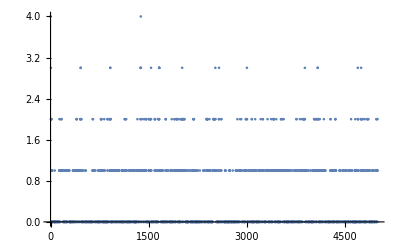

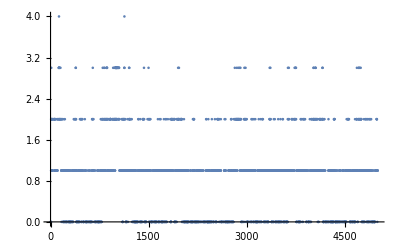

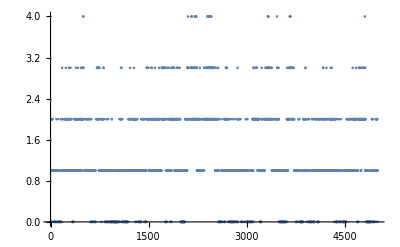

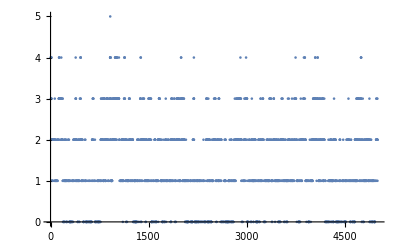

```mathematica
ListPlot[mmvst,PlotRange->All]
ListPlot[Ndvst,PlotRange->All]
ListPlot[Nphivst,PlotRange->All]
ListPlot[mtotvst,PlotRange->All]
```

```mathematica
Joinlists[list1_,list2_]:=
Table[{list1[[i]],list2[[i]]},{i,1,Length[list1]}];

showDs[positions_]:=Module[{lst1,lst2,lst3,pos1,pos2,pos3,mk1,mk2,mk3,plt1,plt2,plt3},

{pos1,pos2}=positions;
pos3=Complement[Table[i,{i,1,5}],pos1,pos2];

lst1=Joinlists[pos1,Table[0,{i,1,Length[pos1]}]];
lst2=Joinlists[pos2,Table[0,{i,1,Length[pos2]}]];
lst3=Joinlists[pos3,Table[0,{i,1,Length[pos3]}]];

mk1=Graphics[{Black,Disk[]}];
mk2=Graphics[{Black,Thick,Circle[]}];
mk3=Graphics[{Green,Rectangle[]}];

plt1=ListPlot[lst1,PlotRange->{{0.8,5.2},{-0.2,+0.2}},PlotMarkers->{mk1,0.1},Axes->{True,False},ImageSize->Large];
plt2=ListPlot[lst2,PlotRange->{{0.8,5.2},{-0.2,+0.2}},PlotMarkers->{mk2,0.1},Axes->{True,False},ImageSize->Large];
plt3=ListPlot[lst3,PlotRange->{{0.8,5.2},{-0.2,+0.2}},PlotMarkers->{mk3,0.1},Axes->{True,False},ImageSize->Large];
Show[plt1,plt2,plt3]
];
DPhis=Joinlists[Dsvst,Phisvst];
```

```mathematica
frames=100;
x=showDs/@DPhis[[1;;frames]];
tau=Table[times[[i+1]]-times[[i]],{i,1,frames}];
slides=Table[Column[{x[[i]],
Grid[{
{"total time elapsed= ",times[[i]]},
{"Next Quantum jump after τ = ",tau[[i]]}}]},Alignment->Left],{i,1,frames}];
Export["/Users/panda/repos/transport-code/anim-timed.gif",slides,"DisplayDurations"->tau/2,"AnimationRepetitions"->Infinity]
```

```mathematica
Export["/Users/panda/repos/transport-code/anim.gif",x]
```

/Users/panda/repos/transport-code/anim.gif

/Users/panda/repos/transport-code/tttt.gif

```mathematica
(*Manipulate[
Column[{x[[i]],
Grid[{{"τ = ",times[[i+1]]-times[[i]]}}]},Alignment->Left],{i,1,frames}]*)
```

```mathematica
(*anim=ListAnimate[x,2]*)
```

```mathematica
(*Export["/Users/panda/repos/transport-code/amin.gif",x]*)
```

/Users/panda/repos/transport-code/amin.gif

```mathematica
(*Dynamics of electrons and holes (disk and circle) with neutral molecules (square) in a metal-metal organic microcavity in strong light matter coupling regime....my code is finally working!*)
```

```mathematica
mtot=mvst+Length/@Dsvst;
nt=2000;
x=showDs/@DPhis[[1;;nt]];
```

$Aborted

```mathematica
Manipulate[
Column[{x[[i]],
Grid[{{"m = ",mvst[[i]]},{"m+N_d = ",mtot[[i]]}}]},Alignment->Left],{i,1,nt,1},ContentSize->{600, 460}]
```

```mathematica
Manipulate[
Column[{x[[i]],
Grid[{{"m = ",mvst[[i]]}},ItemStyle->Directive[FontSize->70,Red]]},Alignment->Left],{i,1,nt,1},ContentSize->{600,500}]
```

```mathematica
Mean[mvst]//N
StandardDeviation[mvst]//N
```

0.50941

0.681353

```mathematica
lenD=Length/@Dsvst;
Mean[lenD]//N
StandardDeviation[lenD]//N

lenp=Length/@Phisvst;
Mean[lenp]//N
StandardDeviation[lenp]//N
```

0.877875

0.811615

1.26432

0.934451

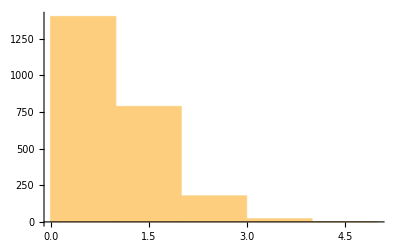

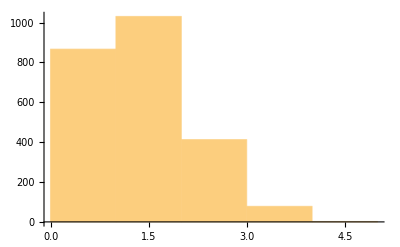

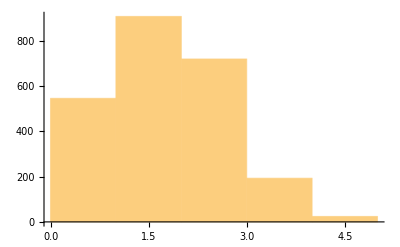

```mathematica
Histogram[mvst,5,PlotRange->All]
Histogram[lenD,5,PlotRange->All]
Histogram[lenp,5,PlotRange->All]
```